# Casimir Optimization Mathematica 9 All Figures

Keep this launcher in the same folder as Casimir_Optimization_Mathematica9_Final.m. Evaluate the three input cells in order. RunStudy[] displays manuscript Figures 2 through 7 inline and also saves each one as a PDF in figures_mathematica9_final.

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"Casimir_Optimization_Mathematica9_Final_2.m"}]]
```

Definitions loaded. Execute SelfTest[] for a quick check and RunStudy[] for the full optimization.

```mathematica
SelfTest[]
```

Self-test Pinf(GaAs, eta=.95) = 3.65028 mPa (reference ~3.65028 mPa)

Self-test leakage(b=13.5 um) = 0.00017737 (reference ~1.77e-4)

Self-test equilibrium indicator = 0.001 (reference 1e-3)

SELF-TEST PASSED. It is safe to execute RunStudy[].

True

--- Robust nonequilibrium Casimir optimization (Mathematica 9) ---

Adachi KK completion: eps0Interband = 9.59699, deltaUV = 1.29301

Emission-only thickness at 10^-3 = 10.4476 um

Adopted thickness = 13.5 um

Leakage at adopted b = 0.00017737

Equilibrium coupling indicator = 0.001

Best feasible coarse point: a = 1.35 um, eta = 0.945, J = 2.25608 mPa

OPTIMUM: aL=aR = 1.35122 um; eta = 0.945; b = 13.5 um

Robust bilateral pressure = 2.25684 mPa

Active uncertainty point {delta a [nm], delta eta} = {10.,-0.005}

Nominal {Peq, PPW, PEW, Ptotal} mPa = {-0.18418,3.24196,-0.00121028,3.05657}

Robust cavity excess = 0.181162 mPa

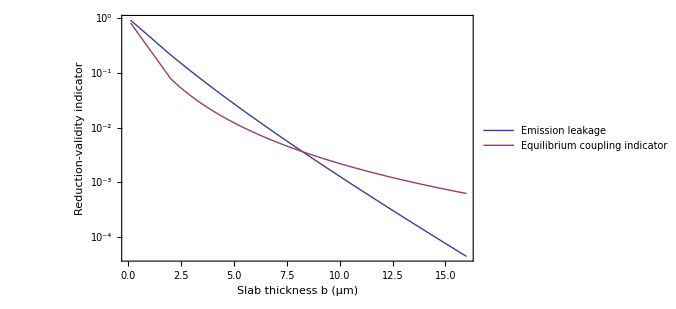

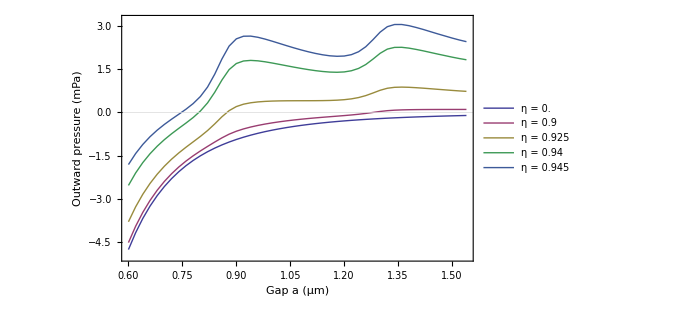

-Graphics-

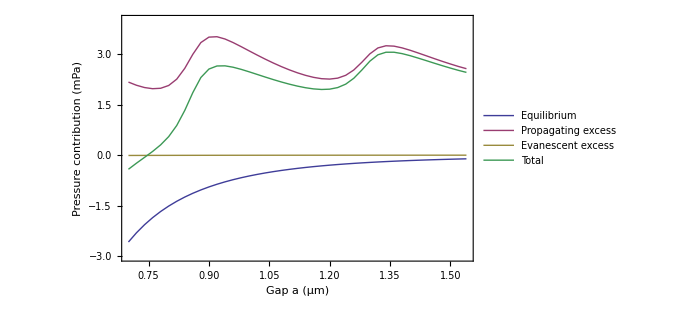

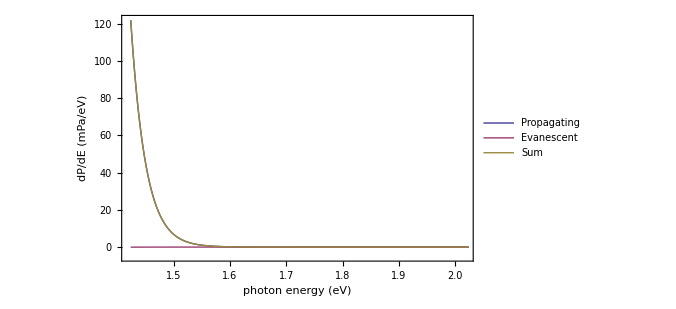

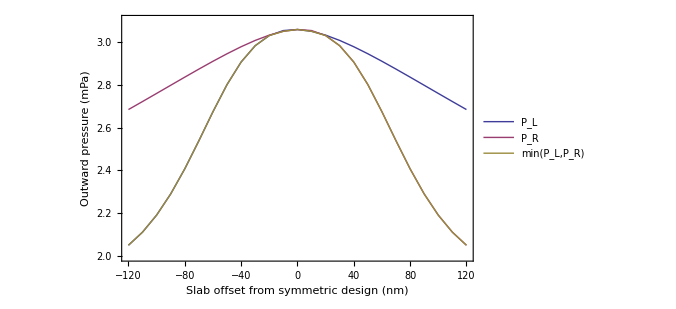

Study complete. CSV data: C:\Users\mrkho_000\Desktop\PRE 2026\New optimization version\data_mathematica9_5_final

Figures: C:\Users\mrkho_000\Desktop\PRE 2026\New optimization version\figures_mathematica9_5_final

{1.35122×10^-6,0.945,0.0000135,0.00225684,{-0.00010873,0.00256211,-7.77133×10^-7,0.0024526}}

```mathematica
RunStudy[]
```

## Finite Slab Validation

```mathematica
RunFiniteSlabValidation[]
```

point | aL_um | aR_um | eta | P_reduced_mPa | P_finite_L_mPa | P_finite_R_mPa | P_finite_min_mPa | Delta_min_mPa | Abs_rel_percent
nominal | 1.35122 | 1.35122 | 0.945 | 3.05657 | 3.05655 | 3.05655 | 3.05655 | -0.0000267537 | 0.000875286
active worst case | 1.34122 | 1.36122 | 0.94 | 2.25684 | 2.25681 | 2.2568 | 2.2568 | -0.0000361787 | 0.00160307

Finite-slab validation written to C:\Users\mrkho_000\Desktop\PRE_2026\New_optimization_version\data_mathematica9_final\finite_slab_validation.csv

{{nominal,1.35122,1.35122,0.945,3.05657,3.05655,3.05655,3.05655,-0.0000267537,0.000875286},{active worst case,1.34122,1.36122,0.94,2.25684,2.25681,2.2568,2.2568,-0.0000361787,0.00160307}}

## Continuous Band - Gap Optimization

```mathematica
RegenerateBandGapOptima[]
```

eta | EgOpt_eV | PinfOpt_mPa
0.94 | 1.2292 | 2.13906
0.945 | 1.34357 | 2.76247
0.95 | 1.48079 | 3.65757

Continuous band-gap optima written to C:\Users\mrkho_000\Desktop\PRE_2026\New_optimization_version\data_mathematica9_final\bandgap_optima.csv

{{0.94,1.2292,2.13906},{0.945,1.34357,2.76247},{0.95,1.48079,3.65757}}